```mathematica
n=3;
XData={1,3,5,7};
YouData={7, n, √n, 2*n};
MatrixForm[XData]
MatrixForm[YouData]
polin=∑_(i=1)^4 YouData[[i]]*∏_(j=1)^4 If[i≠j,(x-XData[[j]])/(XData[[i]]-XData[[j]]),1];
lgr2[x_]:=Collect[polin,x];
lgr2[x]
```

(1
3
5
7)

(7
3
√3
6)

55/8+(21 √3)/16+(4/3-(31 √3)/16) x+(-11/8+(11 √3)/16) x^2+(1/6-(√3)/16) x^3

```mathematica
plot=Plot[{lgr2[x]},{x,0,6}, PlotLabels->"Expressions"];
dots=ListPlot[Table[{N[XData[[i]]],N[YouData[[i]]]},{i,1,4}]];"Построение графика многочлена и точек";
Show[plot,dots]
```

-Graphics-

```mathematica
"Вычислени пропущенных точек таблицы";
N[Collect[polin,x]/.x->2]
```

4.83373

```mathematica
N[Collect[polin,x]/.x->4]
```

1.84928

```mathematica
N[Collect[polin,x]/.x->6]
```

2.9988

```mathematica
XData={1,2,3,4,5,6,7};
YouData={7,4.833734122634726, n,1.8492785792574935, √n,2.9987976320958216, 20/n};
plot=Plot[{lgr2[x]},{x,1,7}, PlotLabels->"Expressions"];
dots=ListPlot[Table[{N[XData[[i]]],N[YouData[[i]]]},{i,1,7}]];"Построение графика многочлена и всех точек, кроме последних двух месяцев";
Show[plot,dots]
```

-Graphics-

```mathematica
"Построение таблицы значений, кроме последних 2 месяцев";
MatrixForm[XData]
MatrixForm[N[YouData]]
```

(1
2
3
4
5
6
7)

(7.
4.83373
3.
1.84928
1.73205
2.9988
6.66667)

```mathematica
"Построение апроксимаций 1, 2 и 4 степени и отображение их на плоскости";
data={{1, 7},{2,4.833734122634726},{3,3},{4, 1.8492785792574935},{5,1.7320508075688772},{6,2.9987976320958216},{7,6.666666666666667}}
"Первая степень:" 
gr[x_]=Fit[data,{1,x},x]
"Вторая степень:"
gr1[x_]=Fit[data,{1,x,x^2},x]
"Четвертая степень:"
gr2[x_]=Fit[data,{1,x,x^2,x^3,x^4},x]
Gr1:=Plot[gr[x],{x,1,9}]
Gr2:=Plot[gr1[x],{x,1,9}]
Gr3:=Plot[gr2[x],{x,1,9}]
```

{{1,7},{2,4.83373},{3,3},{4,1.84928},{5,1.73205},{6,2.9988},{7,6.66667}}

Первая степень:

4.85976-0.212065 x

Вторая степень:

11.5369-4.6635 x+0.556429 x^2

Четвертая степень:

9.62451-2.86859 x+0.288007 x^2-0.0442801 x^3+0.00757576 x^4

```mathematica
Show[plot,dots,Gr1,Gr2,Gr3]
```

-Graphics-

```mathematica
"Прогнозируемые значения графика аппроксимации 1 степени в 9 и 8 месяце";
N[Collect[gr[x],x]/.x->9]
```

2.95118

```mathematica
N[Collect[gr[x],x]/.x->8]
```

3.16324

```mathematica
"Таблица значений для графика аппроксимации 1 степени в каждом месяце"
Xgrdata={};
Ygrdata={};
For[i=1,i≤9,i++,
xgrdata[i]=i;
Xgrdata=Append[Xgrdata,xgrdata[i]];
ygrdata[i]=gr[i];
Ygrdata=Append[Ygrdata,ygrdata[i]];]
```

Таблица значений для графика аппроксимации 1 степени в каждом месяце

```mathematica
MatrixForm[Xgrdata]
MatrixForm[Ygrdata]
```

(1
2
3
4
5
6
7
8
9)

(4.6477
4.43563
4.22357
4.0115
3.79944
3.58737
3.37531
3.16324
2.95118)

Таблица значений для графика аппроксимации 4 степени в каждом месяце

(1
2
3
4
5
6
7
8
9)

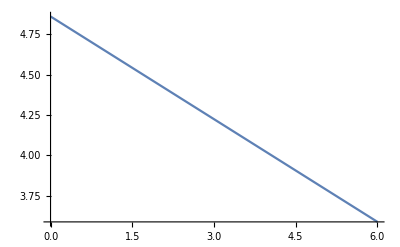
((-Graphics-)[1]
(-Graphics-)[2]
(-Graphics-)[3]
(-Graphics-)[4]
(-Graphics-)[5]
(-Graphics-)[6]
(-Graphics-)[7]
(-Graphics-)[8]
(-Graphics-)[9])

```mathematica
"Таблица значений для графика аппроксимации 4 степени в каждом месяце"
X1grdata={};
Y1grdata={};
For[i=1,i≤9,i++,
x1grdata[i]=i;
X1grdata=Append[X1grdata,x1grdata[i]];
y1grdata[i]=gr2[i];
Y1grdata=Append[Y1grdata,y1grdata[i]];]

MatrixForm[X1grdata]
MatrixForm[Y1grdata]
```